```mathematica
ClearAll["Global`*"];
(*____________________________ General Principles ____________________________*)
(*NOTE: Use units of mm for all lengths, uL/min for all volumetric flow rates.*)
(*NOTE: Impedance in this context will have units of  [R]=[mass]/([time]*[length]^4), AKA 'Acoustic' Ohms. 1 Acoustic Ohm ⧦ kg/(s*m^4)*)
nmin=1; dn=2; (*These are fixed for the sum of Rrect. dn is 2 because the sum is odd*)
Subscript[μ, w] = .7978; (* Dynamic Viscocity of water at 30°C in units of [mPa*s] converted to [kg/(mm s)], [mPa*s]=10^-3[(N s)/m^2]=10^-3[kg/(m s)]= [kg/(mm s)] *)
Subscript[ρ, w]  =0.99567*10^-6; (* Density of water at 30°C in units of [g/cm^3] converted to [kg/mm^3], [g/cm^3]=10^-6[kg/mm^3] *)

(* Rrect~ Resistance of Rectangular channel. See Beebe et al.,2002 *)
Rrect[μ_,h_,w_,L_,nmax_] := ((12μ*L)/(w*h^3))*(1-h/w(192/π^5*Sum[1/n^5*Tanh[(n*π*w)/(2h)],{n,nmin,nmax,dn}]))^-1; 
(* Hagen-Poiseuille Equation for resistance of circular channel. *)
Rcirc[μ_,r_,L_] := (8μ*L)/(π*r^4);
(* Example Approximate form: high aspect ratio w<<h or h<<w *)
FullSimplify[Rrect[μ,h,w,L,0]];Reyn[ρ_,μ_,Pwet_,Q_] := (4ρ*Q)/(60*μ*Pwet); (* Wetted perimeter in mm. Q is usually [μL/min], equation needs [mm^3/s]. [μL/min]= (1/60)[mm^3/s]*)
```

```mathematica
(*____________________________ First Designs - 01/10/2021 ____________________________*)
(*Main chamber resistance. μ ignored in ratios*)
Rcham[h_,w_,L_] :=Rrect[μ,h,w,L,1]/μ;
(*Main chamber resistance. μ ignored in ratios*)
Ralt[h_,w_,L_] :=Rrect[μ,h,w,L,3]/μ;
(*Input/Output line resistance. μ ignored in ratios*)
Rput[r_,L_] :=Rcirc[μ,r,L]/μ;

RM=Rcham[10^-2,3.0,3.0];(*3x3mm medium chamber resistance (wxL)*)
RL=Rcham[10^-2,6.4,3.4];(*3.4x6.4mm large chamber resistance (wxL)*)
(*05/19/21 weird display error here in scientific notation, but number correct*)

Ra1 = Ralt[.2,1,5.2] ;(*Resistance of alternate channel segments*)
Ra2 = Ralt[.2,1.6,4.4];(*Resistance of alternate channel segments*)
Ra =(Ra2+2*Ra1)/2 ; (* Total Resistance of both alt flow channels in parallel.*)

Rin =Rput[.64/2,285.0];(*Input line resistance.*)
Rout =Rput[.64/2,285.0];  (*Output line resistance.*)

(*For given chamber resistance Rc and desired chamber flow rate Qc, returns totalflow rate Qt that should be sourced from syringe pump*)
Qt[Qc_,Rc_] :=(Rc/Ra +1)*Qc; 
(*Finds ratio between chamber flow rate and alternate channel flow rate. (Qr=Qa/Qc=Rc/Ra)*)
Qr[Rc_] := Rc/Ra;
```

Source flow for Medium chamber: Q=1.07821

Flow Ratio: Qa/Qc=1077.21

Source flow for Large chamber: Q=0.572629

Flow Ratio: Qa/Qc=571.629

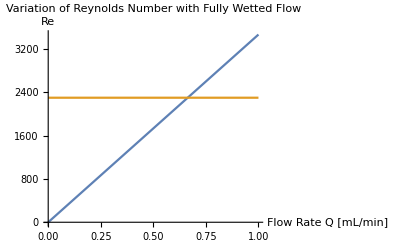

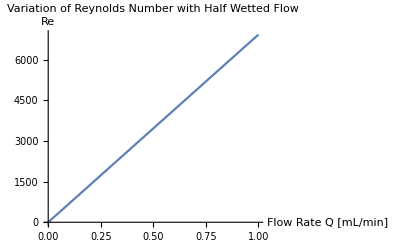

```mathematica
(*____________________________ Laminar Flow Considerations ____________________________*)
(*For medium chamber*)
Print["Source flow for Medium chamber: Q=",Qt[10^-3,RM]]
Print["Flow Ratio: Qa/Qc=", Qr[RM]]
(*For Large chamber*)
Print["Source flow for Large chamber: Q=",Qt[10^-3,RL]]
Print["Flow Ratio: Qa/Qc=",Qr[RL]]
Plot[{Reyn[Subscript[ρ, w],Subscript[μ, w],2.4,Q],2300},{Q,0,10^11},PlotLabel->"Variation of Reynolds Number with Fully Wetted Flow",AxesLabel->{"Flow Rate Q [mL/min]","Re"}] (* Reynolds number assuming fully wetted perimeter*)
Plot[Reyn[Subscript[ρ, w],Subscript[μ, w],1.2,Q],{Q,0,10^11},PlotLabel->"Variation of Reynolds Number with Half Wetted Flow",AxesLabel->{"Flow Rate Q [mL/min]","Re"}](* Reynolds number assuming half wetted perimeter*)
(*If math here is correct you would have to force ~10^6 Litres a second through the alt channels for the Laminar regime to break.*)
```